# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-11-01

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-25

```mathematica
states=Union[seqData[[All,2]]]
```

{California,Colorado,Connecticut,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Rhode Island,South Carolina,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{California,Colorado,Connecticut,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Rhode Island,South Carolina,Tennessee,Texas,Utah,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{California→{{2022-02-11,1570},{2022-02-12,1181},{2022-02-13,691},{2022-02-14,1500},{2022-02-15,1618},{2022-02-16,2247},{2022-02-17,921},{2022-02-18,843},{2022-02-19,586},{2022-02-20,346},{2022-02-21,214},{2022-02-22,353},{2022-02-23,11},{2022-02-24,0},{2022-02-25,0}},Colorado→{{2022-02-11,325},{2022-02-12,183},{2022-02-13,118},{2022-02-14,253},{2022-02-15,277},{2022-02-16,199},{2022-02-17,79},{2022-02-18,23},{2022-02-19,15},{2022-02-20,7},{2022-02-21,28},{2022-02-22,24},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Connecticut→{{2022-02-11,77},{2022-02-12,61},{2022-02-13,67},{2022-02-14,179},{2022-02-15,220},{2022-02-16,144},{2022-02-17,171},{2022-02-18,111},{2022-02-19,44},{2022-02-20,43},{2022-02-21,136},{2022-02-22,37},{2022-02-23,18},{2022-02-24,46},{2022-02-25,27}},Florida→{{2022-02-11,274},{2022-02-12,282},{2022-02-13,248},{2022-02-14,145},{2022-02-15,186},{2022-02-16,299},{2022-02-17,251},{2022-02-18,289},{2022-02-19,189},{2022-02-20,86},{2022-02-21,81},{2022-02-22,66},{2022-02-23,5},{2022-02-24,4},{2022-02-25,0}},Georgia→{{2022-02-11,95},{2022-02-12,86},{2022-02-13,80},{2022-02-14,62},{2022-02-15,53},{2022-02-16,83},{2022-02-17,66},{2022-02-18,43},{2022-02-19,36},{2022-02-20,12},{2022-02-21,23},{2022-02-22,13},{2022-02-23,3},{2022-02-24,0},{2022-02-25,0}},Hawaii→{{2022-02-11,21},{2022-02-12,13},{2022-02-13,19},{2022-02-14,22},{2022-02-15,21},{2022-02-16,21},{2022-02-17,21},{2022-02-18,20},{2022-02-19,18},{2022-02-20,14},{2022-02-21,5},{2022-02-22,8},{2022-02-23,3},{2022-02-24,0},{2022-02-25,0}},Idaho→{{2022-02-11,26},{2022-02-12,8},{2022-02-13,6},{2022-02-14,17},{2022-02-15,23},{2022-02-16,11},{2022-02-17,28},{2022-02-18,5},{2022-02-19,6},{2022-02-20,8},{2022-02-21,11},{2022-02-22,16},{2022-02-23,7},{2022-02-24,11},{2022-02-25,0}},Illinois→{{2022-02-11,139},{2022-02-12,119},{2022-02-13,103},{2022-02-14,168},{2022-02-15,104},{2022-02-16,88},{2022-02-17,53},{2022-02-18,75},{2022-02-19,70},{2022-02-20,60},{2022-02-21,85},{2022-02-22,50},{2022-02-23,7},{2022-02-24,3},{2022-02-25,2}},Indiana→{{2022-02-11,55},{2022-02-12,35},{2022-02-13,40},{2022-02-14,29},{2022-02-15,43},{2022-02-16,45},{2022-02-17,43},{2022-02-18,44},{2022-02-19,39},{2022-02-20,10},{2022-02-21,21},{2022-02-22,10},{2022-02-23,1},{2022-02-24,0},{2022-02-25,0}},Kentucky→{{2022-02-11,35},{2022-02-12,14},{2022-02-13,22},{2022-02-14,27},{2022-02-15,34},{2022-02-16,66},{2022-02-17,54},{2022-02-18,28},{2022-02-19,18},{2022-02-20,10},{2022-02-21,16},{2022-02-22,11},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Louisiana→{{2022-02-11,42},{2022-02-12,39},{2022-02-13,23},{2022-02-14,68},{2022-02-15,41},{2022-02-16,47},{2022-02-17,78},{2022-02-18,29},{2022-02-19,11},{2022-02-20,8},{2022-02-21,18},{2022-02-22,5},{2022-02-23,0},{2022-02-24,0},{2022-02-25,2}},Maryland→{{2022-02-11,40},{2022-02-12,56},{2022-02-13,51},{2022-02-14,51},{2022-02-15,40},{2022-02-16,33},{2022-02-17,35},{2022-02-18,34},{2022-02-19,17},{2022-02-20,14},{2022-02-21,13},{2022-02-22,10},{2022-02-23,1},{2022-02-24,2},{2022-02-25,0}},Massachusetts→{{2022-02-11,253},{2022-02-12,289},{2022-02-13,229},{2022-02-14,541},{2022-02-15,536},{2022-02-16,472},{2022-02-17,514},{2022-02-18,290},{2022-02-19,156},{2022-02-20,168},{2022-02-21,261},{2022-02-22,204},{2022-02-23,49},{2022-02-24,201},{2022-02-25,18}},Michigan→{{2022-02-11,79},{2022-02-12,98},{2022-02-13,55},{2022-02-14,71},{2022-02-15,96},{2022-02-16,70},{2022-02-17,58},{2022-02-18,68},{2022-02-19,56},{2022-02-20,27},{2022-02-21,43},{2022-02-22,17},{2022-02-23,0},{2022-02-24,1},{2022-02-25,0}},Minnesota→{{2022-02-11,230},{2022-02-12,141},{2022-02-13,104},{2022-02-14,135},{2022-02-15,197},{2022-02-16,177},{2022-02-17,130},{2022-02-18,117},{2022-02-19,53},{2022-02-20,66},{2022-02-21,61},{2022-02-22,58},{2022-02-23,11},{2022-02-24,1},{2022-02-25,0}},Mississippi→{{2022-02-11,42},{2022-02-12,7},{2022-02-13,4},{2022-02-14,41},{2022-02-15,26},{2022-02-16,29},{2022-02-17,29},{2022-02-18,11},{2022-02-19,5},{2022-02-20,4},{2022-02-21,22},{2022-02-22,8},{2022-02-23,2},{2022-02-24,0},{2022-02-25,0}},Missouri→{{2022-02-11,51},{2022-02-12,51},{2022-02-13,38},{2022-02-14,46},{2022-02-15,18},{2022-02-16,18},{2022-02-17,14},{2022-02-18,11},{2022-02-19,14},{2022-02-20,10},{2022-02-21,13},{2022-02-22,7},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Nebraska→{{2022-02-11,38},{2022-02-12,24},{2022-02-13,22},{2022-02-14,32},{2022-02-15,33},{2022-02-16,37},{2022-02-17,22},{2022-02-18,18},{2022-02-19,16},{2022-02-20,3},{2022-02-21,13},{2022-02-22,8},{2022-02-23,2},{2022-02-24,6},{2022-02-25,1}},Nevada→{{2022-02-11,98},{2022-02-12,43},{2022-02-13,19},{2022-02-14,31},{2022-02-15,30},{2022-02-16,32},{2022-02-17,17},{2022-02-18,17},{2022-02-19,5},{2022-02-20,4},{2022-02-21,11},{2022-02-22,10},{2022-02-23,0},{2022-02-24,4},{2022-02-25,6}},New Jersey→{{2022-02-11,115},{2022-02-12,120},{2022-02-13,77},{2022-02-14,67},{2022-02-15,38},{2022-02-16,101},{2022-02-17,112},{2022-02-18,110},{2022-02-19,57},{2022-02-20,36},{2022-02-21,31},{2022-02-22,35},{2022-02-23,1},{2022-02-24,1},{2022-02-25,0}},New Mexico→{{2022-02-11,93},{2022-02-12,34},{2022-02-13,18},{2022-02-14,39},{2022-02-15,33},{2022-02-16,23},{2022-02-17,47},{2022-02-18,30},{2022-02-19,17},{2022-02-20,4},{2022-02-21,12},{2022-02-22,14},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},New York→{{2022-02-11,211},{2022-02-12,191},{2022-02-13,162},{2022-02-14,272},{2022-02-15,151},{2022-02-16,140},{2022-02-17,137},{2022-02-18,140},{2022-02-19,48},{2022-02-20,43},{2022-02-21,49},{2022-02-22,23},{2022-02-23,30},{2022-02-24,9},{2022-02-25,2}},North Carolina→{{2022-02-11,405},{2022-02-12,249},{2022-02-13,222},{2022-02-14,310},{2022-02-15,154},{2022-02-16,156},{2022-02-17,103},{2022-02-18,75},{2022-02-19,42},{2022-02-20,39},{2022-02-21,44},{2022-02-22,25},{2022-02-23,9},{2022-02-24,0},{2022-02-25,0}},North Dakota→{{2022-02-11,62},{2022-02-12,29},{2022-02-13,21},{2022-02-14,98},{2022-02-15,64},{2022-02-16,39},{2022-02-17,51},{2022-02-18,40},{2022-02-19,10},{2022-02-20,12},{2022-02-21,19},{2022-02-22,31},{2022-02-23,27},{2022-02-24,20},{2022-02-25,15}},Ohio→{{2022-02-11,54},{2022-02-12,19},{2022-02-13,21},{2022-02-14,41},{2022-02-15,40},{2022-02-16,34},{2022-02-17,31},{2022-02-18,20},{2022-02-19,20},{2022-02-20,9},{2022-02-21,16},{2022-02-22,16},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Oregon→{{2022-02-11,100},{2022-02-12,19},{2022-02-13,21},{2022-02-14,72},{2022-02-15,44},{2022-02-16,48},{2022-02-17,24},{2022-02-18,25},{2022-02-19,8},{2022-02-20,17},{2022-02-21,26},{2022-02-22,5},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Pennsylvania→{{2022-02-11,92},{2022-02-12,75},{2022-02-13,35},{2022-02-14,60},{2022-02-15,98},{2022-02-16,94},{2022-02-17,114},{2022-02-18,115},{2022-02-19,65},{2022-02-20,13},{2022-02-21,15},{2022-02-22,19},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Rhode Island→{{2022-02-11,25},{2022-02-12,27},{2022-02-13,11},{2022-02-14,64},{2022-02-15,54},{2022-02-16,51},{2022-02-17,40},{2022-02-18,21},{2022-02-19,3},{2022-02-20,11},{2022-02-21,29},{2022-02-22,7},{2022-02-23,10},{2022-02-24,10},{2022-02-25,0}},South Carolina→{{2022-02-11,34},{2022-02-12,41},{2022-02-13,41},{2022-02-14,23},{2022-02-15,28},{2022-02-16,21},{2022-02-17,15},{2022-02-18,13},{2022-02-19,8},{2022-02-20,4},{2022-02-21,9},{2022-02-22,8},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Tennessee→{{2022-02-11,86},{2022-02-12,76},{2022-02-13,81},{2022-02-14,55},{2022-02-15,74},{2022-02-16,59},{2022-02-17,33},{2022-02-18,43},{2022-02-19,8},{2022-02-20,8},{2022-02-21,8},{2022-02-22,17},{2022-02-23,9},{2022-02-24,0},{2022-02-25,0}},Texas→{{2022-02-11,357},{2022-02-12,206},{2022-02-13,131},{2022-02-14,184},{2022-02-15,124},{2022-02-16,150},{2022-02-17,112},{2022-02-18,165},{2022-02-19,98},{2022-02-20,66},{2022-02-21,82},{2022-02-22,41},{2022-02-23,10},{2022-02-24,0},{2022-02-25,0}},Utah→{{2022-02-11,139},{2022-02-12,83},{2022-02-13,122},{2022-02-14,163},{2022-02-15,169},{2022-02-16,38},{2022-02-17,17},{2022-02-18,13},{2022-02-19,3},{2022-02-20,13},{2022-02-21,10},{2022-02-22,9},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Virginia→{{2022-02-11,91},{2022-02-12,163},{2022-02-13,75},{2022-02-14,90},{2022-02-15,106},{2022-02-16,79},{2022-02-17,49},{2022-02-18,44},{2022-02-19,13},{2022-02-20,7},{2022-02-21,9},{2022-02-22,19},{2022-02-23,0},{2022-02-24,0},{2022-02-25,0}},Washington→{{2022-02-11,194},{2022-02-12,121},{2022-02-13,60},{2022-02-14,247},{2022-02-15,161},{2022-02-16,142},{2022-02-17,23},{2022-02-18,34},{2022-02-19,19},{2022-02-20,13},{2022-02-21,34},{2022-02-22,56},{2022-02-23,22},{2022-02-24,5},{2022-02-25,2}},Wisconsin→{{2022-02-11,94},{2022-02-12,66},{2022-02-13,86},{2022-02-14,117},{2022-02-15,113},{2022-02-16,78},{2022-02-17,82},{2022-02-18,89},{2022-02-19,39},{2022-02-20,38},{2022-02-21,38},{2022-02-22,29},{2022-02-23,14},{2022-02-24,7},{2022-02-25,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

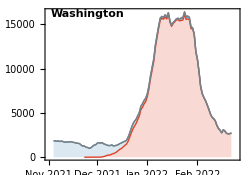

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

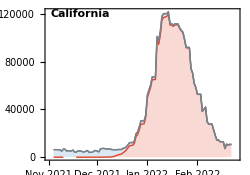
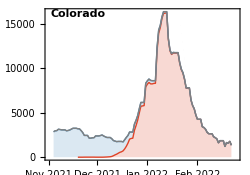
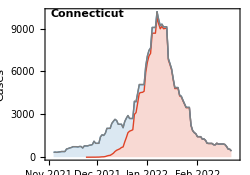
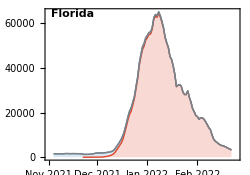
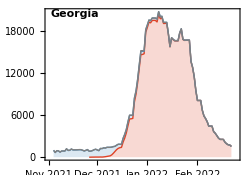
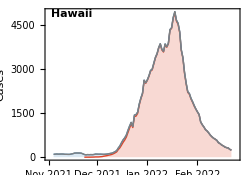
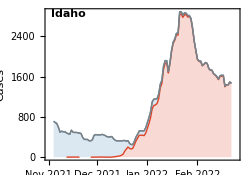
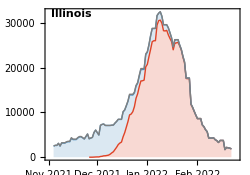
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png